## Домашнее задание №1

### Проектирование сопла Лаваля

##### Дано:

```mathematica
Tz=2780;
pz=0.21 10^6;
H=15;
k=1.4;
R=287.4;
al=6 °;
G=5;
Pf(x_):=Interpolation[Transpose[({{0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 15, 20}, {101330, 98880, 79490, 70130, 61660, 54050, 47210, 41090, 35650, 30790, 26490, 22690, 12110, 5530}})],x,InterpolationOrder->1]
```

Рассчитаем критическую и максимальную скорость :

```mathematica
akr=√((2 k R Tz)/(k+1))
```

965.471

```mathematica
Vmax=√((2 k R Tz)/(k-1))
```

2364.91

Найдем давление на срезе сопла:

```mathematica
psreza=Pf(H)
```

12110

Запишем газодинамическую функцию Пи:

```mathematica
pi(λ_):=(1-((k-1) λ^2)/(k+1))^(k/(k-1))
```

Найдем значение относительной скорости на срезе сопла:

```mathematica
λsopla=λ1/.NSolve[pi(λ1)==psreza/pz,λ1]⟦5⟧
```

1.82883

Плотность по параметрам торможения:

```mathematica
roz=pz/(R Tz)
```

0.262838

Запишем газодинамическую функцию Эпсилон:

```mathematica
eps(l_):=(1-((k-1) l^2)/(k+1))^(1/(k-1))
```

Тогда плотность в критическом сечении будет равна:

```mathematica
rokr=eps(1) roz
```

0.166623

Площадь критического сечения:

```mathematica
Skr=G/(akr rokr)
```

0.0310811

Диаметр критического сечения:

```mathematica
dkr=√((4 Skr)/π)
```

0.198931

Запишем газодинамическую функцию q:

```mathematica
q(l_):=(l eps(l))/(eps(1))
```

Площадь среза сопла (5-го сечения):

```mathematica
S5=Skr/(q(λsopla))
```

0.0826846

Диаметр этого сечения:

```mathematica
d5=√((4 S5)/π)
```

0.324465

Длина геометрического диффузора будет равна:

```mathematica
L=(d5-dkr)/(2 tan(al))
```

0.597185

```mathematica
d={2dkr,dkr,dkr+2 L/3 Tan[al],dkr+4 L/3 Tan[al],d5}
```

{0.397863,0.198931,0.240776,0.28262,0.324465}

```mathematica
S=Pi d^2/4
```

{0.124324,0.0310811,0.0455319,0.062733,0.0826846}

```mathematica
λ=Table[l/.NSolve[ q[l]==S[[2]]/S[[i]],l][[If[i≠1&&i≠2,5,6]]]//Re,{i,1,5}]
```

{0.160192,1.,1.54805,1.72088,1.82883}

```mathematica
tau[l_]:=pi[l]/eps[l]
T=Tz tau[λ]
p=pz pi[λ]
ro=roz eps[λ]
```

{2768.11,2316.67,1669.63,1407.87,1230.33}

{206873.,110939.,35256.4,19410.4,12110.}

{0.260036,0.166623,0.0734732,0.0479716,0.0342479}

```mathematica
azv=√(k R T)
```

{1055.36,965.471,819.63,752.643,703.589}

```mathematica
v=akr*λ
```

{154.661,965.471,1494.6,1661.46,1765.68}

```mathematica
naz={" ","d, м","λ","T, K","P, Па","ρ, кг/(:043c)^3","v, м/с","a_(:0437:0432), м/с"};
sech={"сечение №1","сечение №2","сечение №3","сечение №4","сечение №5"};
```

```mathematica
raund[x_]:=Round[1000x]/1000//N
Column[{Row[{"P^*=",pz," Па   T^*=",Tz," К   H=",H," км   v_max=",raund@Vmax," м/с   a_(:043a:0440)=",raund@akr," м/с   L=",raund@L," м"}],Grid[Flatten[{{naz},Flatten[{{sech},Round[1000{d,λ,T,p,ro,v,azv}]/1000//N},1]ᵀ},1]ᵀ,Frame->All,Background->{None,{{LightGray,None}}},Spacings->{3, 2}]}]
```

P^*=210000. Па   T^*=2780 К   H=15 км   v_max=2364.91 м/с   a_кр=965.471 м/с   L=0.597 м
  | сечение №1 | сечение №2 | сечение №3 | сечение №4 | сечение №5
d, м | 0.398 | 0.199 | 0.241 | 0.283 | 0.324
λ | 0.16 | 1. | 1.548 | 1.721 | 1.829
T, K | 2768.11 | 2316.67 | 1669.63 | 1407.87 | 1230.34
P, Па | 206873. | 110939. | 35256.4 | 19410.4 | 12110.
ρ, кг/м^3 | 0.26 | 0.167 | 0.073 | 0.048 | 0.034
v, м/с | 154.661 | 965.471 | 1494.6 | 1661.46 | 1765.68
a_зв, м/с | 1055.36 | 965.471 | 819.63 | 752.643 | 703.589

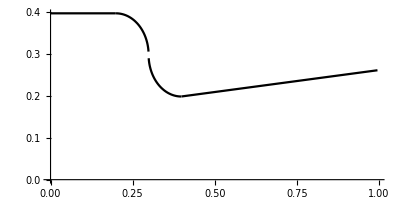

```mathematica
dd[x_]:=Piecewise[{{d[[1]],0<x<=L/3},{√(-(x-L/3)^2+dkr^2/4)+d[[1]]-dkr/2,L/3+dkr/2≥ x≥ L/3},{-√(-(x-L/3-dkr)^2+dkr^2/4)+d[[2]]+dkr/2,L/3+dkr≥ x>=L/3+dkr/2},{d[[2]]+Tan[al](x-L/3-dkr),x≥ L/3+dkr}},0]
Plot[dd[x],{x,0,4L/3+dkr},PlotRange->{0,d[[1]]},AspectRatio->1/2,PlotStyle->Black]
```

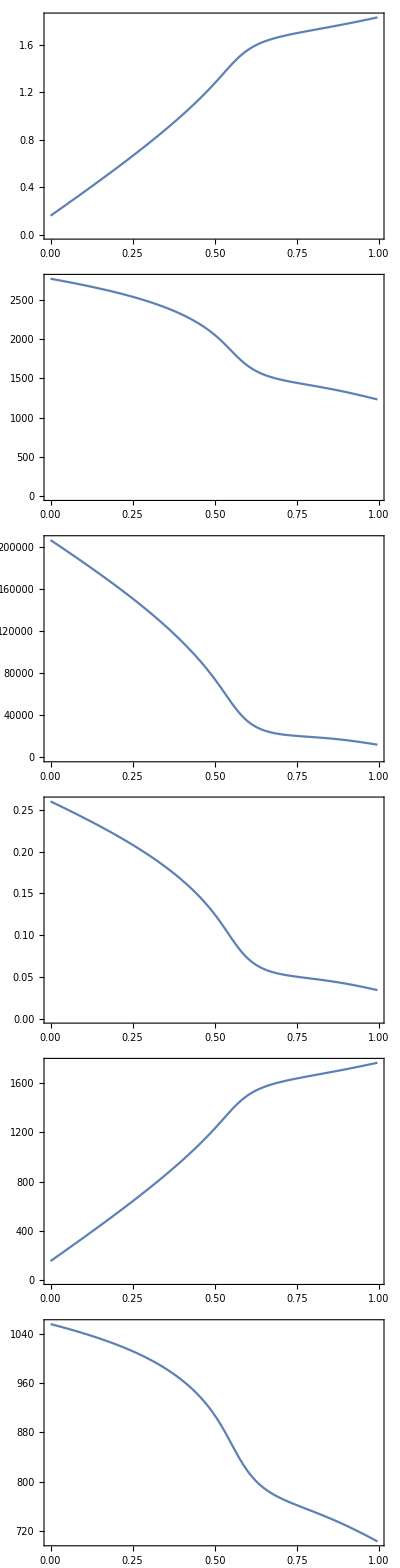

```mathematica
otv={λ,T,p,ro,v,azv};
Column[Table[ListLinePlot[{{0,L/3+dkr,2L/3+dkr,3L/3+dkr,4L/3+dkr},otv[[i]]}ᵀ,PlotRange->{{0,4L/3+dkr},Automatic},InterpolationOrder->4,Frame->True,ImageSize->400,Ticks->Automatic],{i,1,Length[otv]}]]
```

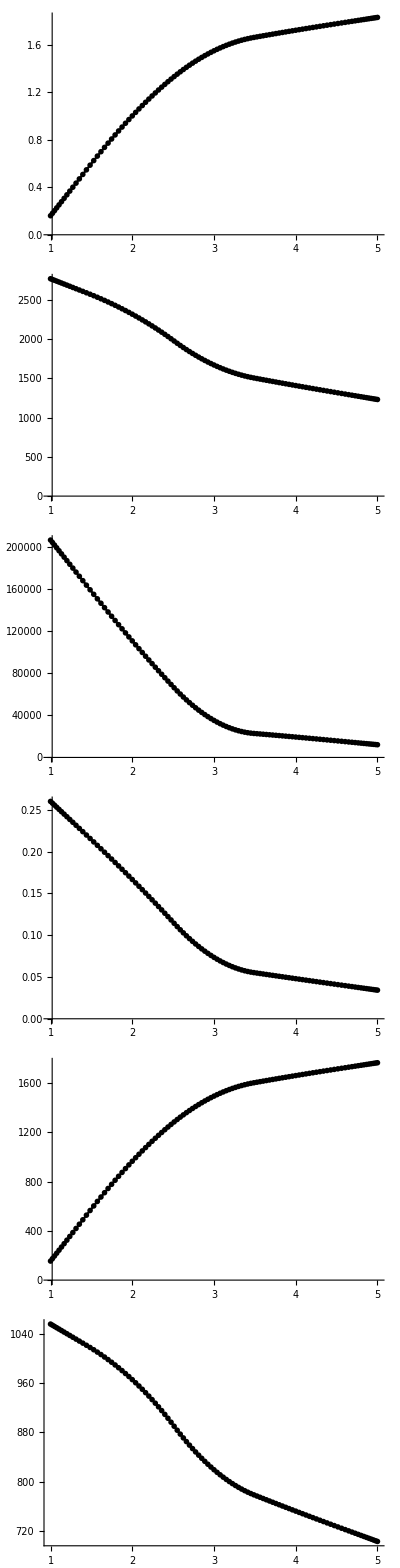

```mathematica
otv={λ,T,p,ro,v,azv};
Column[Table[ListLinePlot[otv[[i]],PlotRange->{{1,5},Automatic},InterpolationOrder->2,ImageSize->400,PlotTheme->"Monochrome"],{i,1,Length[otv]}]]
```